## Simplifying the integrand by a polynomial:

```mathematica
n1=Series[Sin[x],{x,0,6}]
```

x-x^3/6+x^5/120+O[x]^7

```mathematica
n2 = Series[Cos[x], {x,0,6}]
```

1-x^2/2+x^4/24-x^6/720+O[x]^7

```mathematica
n3 = Series[Exp[-1/x], {x,0,6}]
```

ⅇ^(-1/x+O[x]^8)

```mathematica
n4 = Series[Exp[-r/Cos[x]], {x,0,6}]
```

ⅇ^-r-1/2 (ⅇ^-r r) x^2+1/24 ⅇ^-r r (-5+3 r) x^4-1/720 (ⅇ^-r r (61-75 r+15 r^2)) x^6+O[x]^7

Here, r is the optical density

ⅇ^-r-1/2 (ⅇ^-r r) x^2+1/24 ⅇ^-r r (-5+3 r) x^4-1/720 (ⅇ^-r r (61-75 r+15 r^2)) x^6+O[x]^7

```mathematica
n5= Series[Sin[x]*Cos[x], {x,0,11}]
```

x-(2 x^3)/3+(2 x^5)/15-(4 x^7)/315+(2 x^9)/2835-(4 x^11)/155925+O[x]^12

```mathematica
numerator = 1.334*π*n5
```

4.19088 x-2.79392 x^3+0.558785 x^5-0.0532176 x^7+0.00295653 x^9-0.00010751 x^11+O[x]^12

```mathematica
n6=Series[(1.334*Sin[x])^2,{x,0,12}]
```

1.77956 x^2-0.593185 x^4+0.0790914 x^6-0.00564938 x^8+0.000251084 x^10-7.6086×10^-6 x^12+O[x]^13

```mathematica
denominator = (1-n6)^5
```

1-8.89778 x^2+34.6341 x^4-77.8629 x^6+112.861 x^8-112.145 x^10+79.86 x^12+O[x]^13

```mathematica
frac = numerator/denominator
```

4.19088 x+34.4956 x^3+162.346 x^5+576.052 x^7+1715.83 x^9+4533.5 x^11+O[x]^12

```mathematica
eqn = frac*n4
```

4.19088 ⅇ^-r x+(34.4956 ⅇ^-r-2.09544 ⅇ^-r r) x^3+(162.346 ⅇ^-r-17.2478 ⅇ^-r r+0.17462 ⅇ^-r r (-5+3 r)) x^5+(576.052 ⅇ^-r-81.1729 ⅇ^-r r+1.43732 ⅇ^-r r (-5+3 r)-0.00582067 ⅇ^-r r (61-75 r+15 r^2)) x^7+O[x]^8

Eqn is our simplified polynomial approximation to our integral

## Analyzing the accuracy of the polynomial approximation and the actual integral:

We are analysing the situation at the an arbitrary optical density (r value) of 1.

```mathematica
approx = 1.5417402846210897 x+11.919368870971237 x^3+53.2501009183317 x^5+180.99634734711293 x^7+O[x]^8
```

1.54174 x+11.9194 x^3+53.2501 x^5+180.996 x^7+O[x]^8

```mathematica
actual = (1.334*Pi*Sin[x]*Cos[x]*Exp[-1/Cos[x]])/(1-(1.334*Sin[x])^2)^(1/2)
```

(4.19088 ⅇ^(-Sec[x]) Cos[x] Sin[x])/(√(1-1.77956 Sin[x]^2))

```mathematica
ratio = actual/approx
```

1.-8.008 x^2+27.608 x^4-53.9649 x^6+O[x]^7

Plan is to see if the actual and  approx functions are well aligned or not. For some reason mathematica doesn’t let me plot approx

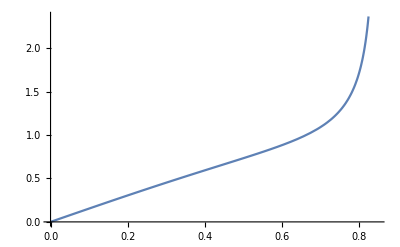

```mathematica
p1 = Plot[actual, {x,0, ArcSin[1/1.334]}]
```

```mathematica
p1 = Plot[approx, {x,0, ArcSin[1/1.334]}]
```

SeriesData::ssdn: Attempt to evaluate a series at the number 0.0000173131. Returning Indeterminate.

SeriesData::ssdn: Attempt to evaluate a series at the number 0.0173131. Returning Indeterminate.

SeriesData::ssdn: Attempt to evaluate a series at the number 0.034609. Returning Indeterminate.

General::stop: Further output of SeriesData::ssdn will be suppressed during this calculation.

-Graphics-

However, MATLAB plotted the ratio function. From the plot we can see that our approximation is not very good as it only valid till 0.2 rads.

Further plan is to use higher order terms and see if there is better approximation polynomial available. 

Another plan is to use analytical methods to simplify our integral. (Assuming there is any)